# Non-trivial Equilibria Stability Analysis

## Finding Non-Trivial Equilibria & Plotting equilibria with prey birth rate (b) as control

```mathematica
(*Finding the equilibria system*)
ClearAll[phi,psi,A,B,phiPrime,psiPrime,APrime,BPrime,dA,dB,p,b,m,s, A1, A2, B1, B2, NumA1, NumA2, NumB1, NumB2, NumEigAtEq1, NumEigAtEq2, EigAtEq1, EigAtEq2];
F[A_,B_]:=-dA*A+m*B+2*p*A*B
G[A_,B_]:=B*(-dB-m-2*p*A+2*b-2*b*(A+B))
M={{dA*(1-B)+p*B,dA*A,0,0},{dB*B,dB*(1-A)-b*(A+B),0,0},{0,0,1,0},{0,0,0,1}};

(*Vector on the right-hand side*)
RHS={-s*phi-F[A,B],-s*psi-G[A,B],phi,psi};
(*Isolating derivatives on the right hand-side {phiPrime,psiPrime,APrime,BPrime}*)
DynSis= Inverse[M].RHS;
(*Solve for derivatives when {phi',psi',A',B'}=0*)
EquilibriaEquation = DynSis == {0,0,0,0}
```

Clea

{((-A b-b B+dB-A dB) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-(A dA (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),-(B dB (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+((dA-B dA+B p) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),phi,psi}=={0,0,0,0}

```mathematica
{((-A b-b B+dB-A dB) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-(A dA (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),-(B dB (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+((dA-B dA+B p) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),phi,psi}=={0,0,0,0}
```

{((-A b-b B+dB-A dB) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-(A dA (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),-(B dB (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+((dA-B dA+B p) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),phi,psi}=={0,0,0,0}

```mathematica
(*Solving the equilibia equations*)
equilibria = Solve[EquilibriaEquation, {phi, psi, A, B}];

(*Retrieving the 2 non-trivial equilibria points*)
NonTrivialEq = equilibria[[{2,3}]]
```

{{phi→0,psi→0,A→(4 b dA-2 dA dB-4 dA m-(2 b dA^2)/p-(2 b dA m)/p+(dA √(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/p)/(8 (b dA+dA p)),B→(2 b dA+2 b m+4 b p-2 dB p-√(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/(8 b p)},{phi→0,psi→0,A→(4 b dA-2 dA dB-4 dA m-(2 b dA^2)/p-(2 b dA m)/p-(dA √(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/p)/(8 (b dA+dA p)),B→(2 b dA+2 b m+4 b p-2 dB p+√(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/(8 b p)}}

```mathematica
NumericalParameters = {D -> 0.1, p -> 0.2 , dA -> 0.01, dB ->0.01, m -> 0.001}; 
(*NumericalNonTrivialEq = NonTrivialEq/.NumericalParameters*)
```

```mathematica
(* Extracting A and B from the two non-trivial solutions *)
A1[b_] = (A /. NonTrivialEq[[1]])
B1[b_] = (B /. NonTrivialEq[[1]])
A2[b_] = (A /. NonTrivialEq[[2]])
B2[b_] = (B /. NonTrivialEq[[2]])

(*Finding the equivalent non-trivial solutions with numerical parameters*)
NumA1[b_] := (A /. NonTrivialEq[[1]]) /. NumericalParameters;
NumB1[b_] := (B /. NonTrivialEq[[1]]) /. NumericalParameters;
NumA2[b_] := (A /. NonTrivialEq[[2]]) /. NumericalParameters;
NumB2[b_] := (B /. NonTrivialEq[[2]]) /. NumericalParameters;
```

(4 b dA-2 dA dB-4 dA m-(2 b dA^2)/p-(2 b dA m)/p+(dA √(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/p)/(8 (b dA+dA p))

(2 b dA+2 b m+4 b p-2 dB p-√(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/(8 b p)

(4 b dA-2 dA dB-4 dA m-(2 b dA^2)/p-(2 b dA m)/p-(dA √(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/p)/(8 (b dA+dA p))

(2 b dA+2 b m+4 b p-2 dB p+√(-16 b (2 b dA-dA dB-dA m) p+(-2 b dA-2 b m-4 b p+2 dB p)^2))/(8 b p)

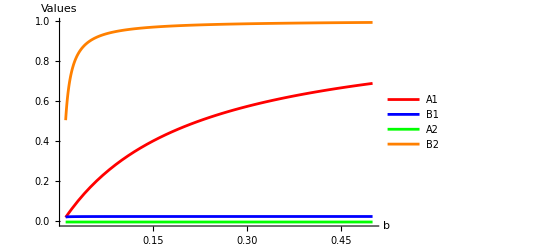

```mathematica
Plot[{NumA1[b], NumB1[b], NumA2[b], NumB2[b]}, {b, 0.01, 0.5},
     PlotLegends -> {"A1", "B1", "A2", "B2"},
     PlotStyle -> {Red, Blue, Green, Orange},
     AxesLabel -> {"b", "Values"},
     PlotRange -> All]
```

## Stability Analysis - Computation of the Jacobian & Eigenvalues

```mathematica
(*Jacobian computation & Evalutation At Equilibria*)
JacobianMatrix = D[DynSis,{{phi, psi, A, B}}]
JacAtEq1 = JacobianMatrix /. {phi -> 0, psi ->0, A -> A1[b], B -> B1[b]};
JacAtEq2 = JacobianMatrix /. {phi -> 0, psi ->0,A -> A2[b], B -> B2[b]};
NumJacAtEq1 = JacAtEq1 /. NumericalParameters;
NumJacAtEq2 = JacAtEq2 /. NumericalParameters;
```

{{-((-A b-b B+dB-A dB) s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),(A dA s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),(A B dA (-2 b-2 p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+((-A b-b B+dB-A dB) (dA-2 B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-((-A b-b B+dB-A dB) (-B dA dB+(-b-dB) ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2+((-b-dB) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(A dA (-B dA dB+(-b-dB) ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-(dA (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),((-A b-b B+dB-A dB) (-m-2 A p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-(A dA (-2 b+2 b B+2 b (A+B)+dB+m+2 A p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-((-A b-b B+dB-A dB) (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-(b (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(A dA (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2},{(B dB s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),-((dA-B dA+B p) s)/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p)),-(B dB (dA-2 B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-(B (-2 b-2 p) (dA-B dA+B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(B dB (-B dA dB+(-b-dB) ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-((dA-B dA+B p) (-B dA dB+(-b-dB) ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2,-(B dB (-m-2 A p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+((-2 b+2 b B+2 b (A+B)+dB+m+2 A p) (dA-B dA+B p))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))+(B dB (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2-(dB (A dA-B m-2 A B p-phi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))-((dA-B dA+B p) (-A dA dB+(-b (A+B)+(1-A) dB) (-dA+p)-b ((1-B) dA+B p)) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))^2+((-dA+p) (-B (2 b-2 b (A+B)-dB-m-2 A p)-psi s))/(-A B dA dB+(-b (A+B)+(1-A) dB) ((1-B) dA+B p))},{1,0,0,0},{0,1,0,0}}

## Eigenvalues for Non-Trivial Equilibrium 1 (Predator prevails A1 =1, B1 = 0)

```mathematica
(*Computing the numerical eigenvalues of the resulting numerical jacobian*)
NumEigAtEq1[b_,s_] = Eigenvalues[NumJacAtEq1];

Plot3D[
 Re[NumEigAtEq1[b, s][[1]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen 1 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen1]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
Plot3D[
 Re[NumEigAtEq1[b, s][[2]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen2 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen2]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
Plot3D[
 Re[NumEigAtEq1[b, s][[3]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen3 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen3]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
Plot3D[
 Re[NumEigAtEq1[b, s][[4]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen4 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen4]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

## Eigenvalues for Non - Trivial Equilibrium 2 (Prey prevails, A2= 0, B2 =1)

```mathematica
(*Computing the numerical eigenvalues of the resulting numerical jacobian*)
NumEigAtEq2[b_,s_] = Eigenvalues[NumJacAtEq2];
NumEigAtEq2[0.5, 0.5];

Plot3D[
 Re[NumEigAtEq2[b, s][[1]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen 1 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen1]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
Plot3D[
 Re[NumEigAtEq2[b, s][[2]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen2 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen2]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
Plot3D[
 Re[NumEigAtEq2[b, s][[3]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen3 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen3]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
Plot3D[
 Re[NumEigAtEq2[b, s][[4]]],
 {b, 0, 1}, {s, 0, 1},
 PlotLabel -> "Real part of eigen4 vs b and s",
 AxesLabel -> {"b", "s", "Re[eigen4]"},
 ColorFunction -> "TemperatureMap",
 MeshFunctions -> {#3 &},
 MeshStyle -> {{Thick, Black}}
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»